```mathematica
(*1*)
f[x_]=(Log2[3x+2])/(x+4);
x0=1.13;
```

```mathematica
D1=D[f[x],x]/.x->x0//N
D2=D[f[x],{x,2}]/.x->x0//N
```

0.0641802

-0.112142

```mathematica
h1=0.1;
Delta1=f[x0 + h1]-f[x0];
Delta2=f[x0+2*h1]-2*f[x0+h1]+f[x0];
Delta3=f[x0+3*h1]-3*f[x0+2*h1]+3*f[x0+h1]-f[x0];
D1=1/h1*(Delta1-1/2*Delta2+1/3*Delta3)  // N
D2=1/h1^2*(Delta2-Delta3) // N
```

0.0641242

-0.110038

```mathematica
h2=0.01;
Delta1=f[x0+h2]-f[x0];
Delta2=f[x0+2*h2]-2*f[x0+h2]+f[x0];
Delta3=f[x0+3*h2]-3*f[x0+2*h2]+3*f[x0+h2]-f[x0];
D1prime=1/h2*(Delta1-1/2*Delta2+1/3*Delta3) // N
D2prime=1/h2^2*(Delta2-Delta3) // N
```

0.0641801

-0.112117

```mathematica
(*2*)
```

```mathematica
f2[x_]=Sin[x + Cos[x]];
a = -1;
b = 3;
h=0.2;
Data=Table[{i,(f2[i+h]-f2[i-h])/(2h)},{i,a,b,h}]//N;
Data//TableForm
```

-1. | 1.59989
-0.8 | 1.66778
-0.6 | 1.50228
-0.4 | 1.19973
-0.2 | 0.859176
0. | 0.553262
0.2 | 0.318767
0.4 | 0.16202
0.6 | 0.0706969
0.8 | 0.0252397
1. | 0.00676944
1.2 | 0.00116141
1.4 | 0.0000890113
1.6 | -4.14846×10^-6
1.8 | -0.000213098
2. | -0.00206558
2.2 | -0.0103158
2.4 | -0.0349532
2.6 | -0.0917143
2.8 | -0.200258
3. | -0.379028

```mathematica
f3[x_]=D[f2[x],x];
```

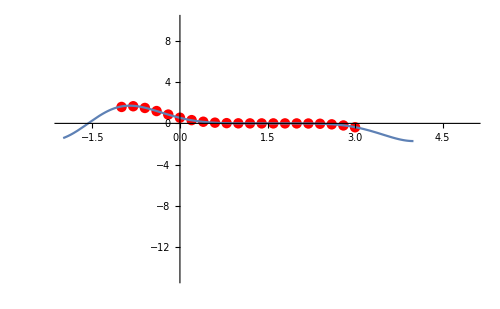

```mathematica
Show[ListPlot[Data,PlotStyle->{Red,PointSize[0.015]}],Plot[f3[x],{x,-2,4}],PlotRange->{{-2,5},{-15,10}}]
```

```mathematica
(*3*)
(* a, n=8 *)
a = 0.7;
b = 2.1;
n=8;
fNEW[x_]=(1+√(2.3x^2+0.2))/(2.4+√(1.6x+1.7));
```

```mathematica
Integrate[fNEW[x],{x,a,b}]//N
```

1.00922

```mathematica
Integral1=0;
Do[Integral1+=(fNEW[a+i*h]+fNEW[a+(i-1)*h])/2,{i,1,n}];
Integral1*=(b-a)/n;
Integral1
```

1.04607

```mathematica
Integral2 = 0;
Do[Integral2+=fNEW[a+i*h],{i,1,n-1}];
Integral2+=(fNEW[a]+fNEW[b])/2;
Integral2*=(b-a)/n;
Integral2
```

1.04167

```mathematica
(* n = 10*)
n = 10;
Integral3=0;
Do[Integral3+=(fNEW[a+i*h]+fNEW[a+(i-1)*h])/2,{i,1,n}];
Integral3*=(b-a)/n;
Integral3
```

1.11856

```mathematica
Integral4 = 0;
Do[Integral4+=fNEW[a+i*h],{i,1,n-1}];
Integral4+=(fNEW[a]+fNEW[b])/2;
Integral4*=(b-a)/n;
Integral4
```

1.1082

```mathematica
Rich1=Integral3+8^2/(10^2-8^2)*(Integral3-Integral1)
```

1.24744

```mathematica
Rich2=Integral4+8^2/(10^2-8^2)*(Integral4-Integral2)
```

1.22649

```mathematica
(*4*)

data={
{0.5,1.2506},
{0.552,1.2938},
{0.604,1.3828},
{0.656,1.4115},
{0.708,1.4927},
{0.76,1.5111},
{0.812,1.5877},
{0.864,1.5993},
{0.916,1.6742},
{0.968,1.6819},
{1.02,1.7575},
{1.072,1.7640},
{1.124,1.8428},
{1.176,1.8501},
{1.228,1.9344},
{1.28,1.9446},
{1.332,2.0366}
};
DataY = {1.2506,
		  1.2938,
		  1.3828,
		  1.4115,
		  1.4927,
		  1.5111,
		  1.5877,
		  1.5993,
		  1.6742,
		  1.6819,
             1.7575,
		  1.7640,
		  1.8428,
		  1.8501,
		  1.9344,
		  1.9446,
		  2.0366};
```

```mathematica
a=0.5;
b=1.332;
n=8;
h=(b-a)/(2n);
```

```mathematica
Sum1=0;
Sum2=0;
Do[Sum1+=DataY[[i]],{i,2,2n,2}];
Do[Sum2+=DataY[[i]],{i,3,2(n-1),2}];
h/3*(DataY[[2n+1]]+DataY[[1]] +4 *Sum1  +2 * Sum2)
```

1.29979

```mathematica
a=0.5;
b=1.332;
n=4;
h=(b-a)/(2n);
Sum1=0;
Sum2=0;
Do[Sum1+=DataY[[i]],{i,3,4n,4}];
Do[Sum2+=DataY[[i]],{i,5,4(n-1),4}];
h/3*(DataY[[4n+1]]+DataY[[1]] +4 *Sum1  +2 * Sum2)
```

1.25738

```mathematica
(*5*)
fNEWNEW[x_]= (Csch[x+3])/(5x+2);
n=7;
a=1.3;
b=2.6;
LegendreP[n,t];
sl=NSolve[LegendreP[n,t]==0,t];
tt=t/.sl;
T=Table[If[i==1,1,(tt[[j]])^(i-1)],{i,n},{j,n}];
MatrixForm[T];
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N;
A=LinearSolve[T,B];
int=(b-a)/2*∑_(i=1)^n A[[i]]*fNEWNEW[(b+a)/2+(b-a)/2*tt[[i]]]
```

0.00183045

```mathematica
NIntegrate[fNEWNEW[x],{x,a,b}]
```

0.00183045